```mathematica
redRandom3 = Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\Redes Difusion\\aleatoria\\red3.graphml"];
```

```mathematica
redRandom4 = Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\Redes Difusion\\aleatoria\\red4.graphml"];
```

```mathematica
redRandom5 = Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\Redes Difusion\\aleatoria\\red5.graphml"];
```

```mathematica
redModelo3 = Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\Redes Difusion\\modelo\\red3.graphml"];
```

```mathematica
redModelo4 = Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\Redes Difusion\\modelo\\red4.graphml"];
```

```mathematica
redModelo5 = Import["C:\\Users\\usuario\\Documents\\Trabajo de Grado II\\Redes Difusion\\modelo\\red5.graphml"];
```

#### Medidas de red de las redes utilizadas Coeficiente de agrupacion promedio (average clustering coefficient) Redes Aleatorias: Red 3, 4 y 5:

```mathematica
N[MeanClusteringCoefficient[redRandom3]]
```

0.172106

```mathematica
N[MeanClusteringCoefficient[redRandom4]]
```

0.144223

```mathematica
N[MeanClusteringCoefficient[redRandom5]]
```

0.146835

#### Redes del Modelo: Red 3, 4 y 5

```mathematica
N[MeanClusteringCoefficient[redModelo3]]
```

0.323306

```mathematica
N[MeanClusteringCoefficient[redModelo4]]
```

0.292395

```mathematica
N[MeanClusteringCoefficient[redModelo5]]
```

0.293706

#### Longitud de Camino Promedio (average shortest path length) Redes Aleatorias: Red 3, 4 y 5

```mathematica
N[MeanGraphDistance[redRandom3]]
```

1.88727

```mathematica
N[MeanGraphDistance[redRandom4]]
```

1.85556

```mathematica
N[MeanGraphDistance[redRandom5]]
```

1.85336

#### Redes del Modelo: Red 3, 4 y 5

```mathematica
N[MeanGraphDistance[redModelo3]]
```

2.02162

```mathematica
N[MeanGraphDistance[redModelo4]]
```

1.87475

```mathematica
N[MeanGraphDistance[redModelo5]]
```

1.85908

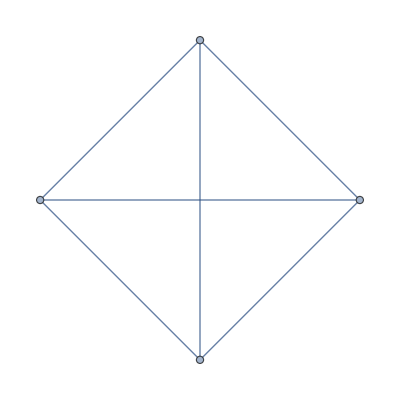

```mathematica
redClique = Graph[{1<->2,2<->3,3<->4,4<->2,3<->1,4<->1}]
```

```mathematica
N[MeanClusteringCoefficient[redClique]]
```

1.

```mathematica
∑_(v=1)^99 v
```

4950

```mathematica
N[MeanGraphDistance[redClique]]
```

1.